# Cornell ERL Injector buncher: Full

```mathematica
root=NotebookDirectory[]
```

/Volumes/user/cem52/erl/CERL/lattice_devel/Phase1B/model/a1/buncher/

```mathematica
tmpdir = "~/Desktop/";
```

```mathematica
outputCavityFilename = "in.buncher_grid.bmad";
outputWallFilename = "in.buncher_wall.bmad";
bmadelename = "in.buncher";

(*Master switch to flip fields*)
FLIP =False;

If[FLIP,
outputCavityFilename = "in.buncher_reverse_grid.bmad";
outputWallFilename = "in.buncher_reverse_wall.bmad";
bmadelename = "in.buncher_reverse";
]
```

## Options

```mathematica
myplotoptions={BaseStyle->{FontSize->15}, Frame->True};
SetOptions[Plot,myplotoptions];
SetOptions[ListPlot,myplotoptions];
SetOptions[ListLogPlot,myplotoptions];
SetOptions[ListVectorPlot,myplotoptions];
SetOptions[ListDensityPlot,myplotoptions];

cLightN = 299792458.;
μ0N = 4. π 10^-7;
```

## Import

```mathematica
griddatrawfilename="buncher_volume_fields.fls";
surfacedatrawfilename="buncher_surface_fields.fls";
```

```mathematica
griddatrawheader= Import[root<>griddatrawfilename, "Table"][[1;;8]];
griddatraw= Import[root<>griddatrawfilename, "Table"][[6;;]];
```

```mathematica
griddatrawheader//Grid
```

::Buncher Cavity, a = 2" | Date:12/15/11.00.00 |  |  |  |  |  |  |  |  | 
Mode | number | 1;Frequency | MHz | 1305.97681;Accuracy | 0. |  |  |  |  | 
R0(CM)= | 0. | Z0(CM)= | 0. | NY= | 90 | NX=100 | DR(CM)= | 0.1 | DZ(CM)= | 0.1
Normalization | V(MeV)= | 0.1 |  |  |  |  |  |  |  | 
R(CM) | Z(CM) | Er(MV/M) | Ez(MV/M) | Hfi(A/M) |  |  |  |  |  | 
0. | 0. | 0. | 1.59248 | 0. |  |  |  |  |  | 
0. | 0.1 | 0. | 1.59245 | 0. |  |  |  |  |  | 
0. | 0.2 | 0. | 1.59233 | 0. |  |  |  |  |  |

```mathematica
(*Raw data only has z≥0. Create the -z points and join*)
griddatR= {1/100*#[[1]], 1/100* #[[2]],10^6* #[[3]], 10^6*#[[4]], μ0N *#[[5]]}&/@griddatraw;
griddatL= {1/100*#[[1]],- 1/100* #[[2]],-10^6* #[[3]], 10^6*#[[4]], μ0N *#[[5]]}&/@Select[griddatraw, #⟦2⟧>0&];
griddat=Join[griddatL,griddatR];
xC=1;
zC=2;
ExC=3;
EzC=4;
ByC=5;

If[FLIP,
flip=Table[1, {5}];
flip⟦zC⟧ = -1;
flip⟦EzC⟧ = -1;
flip⟦ByC⟧ = -1;
griddat=griddat.DiagonalMatrix[flip];
]
```

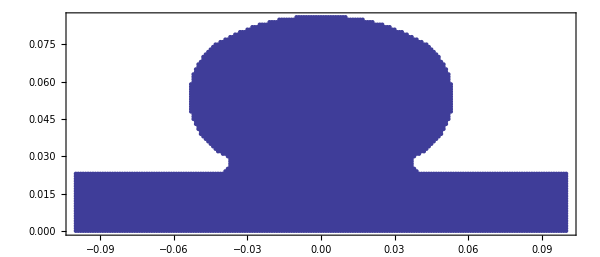

```mathematica
ListPlot[{#[[zC]], #[[xC]]}&/@griddat, ImageSize->600, AspectRatio->Automatic]
```

```mathematica
surfacedatrawheader= Import[root<>surfacedatrawfilename, "Table"][[1;;6]];
surfacedatraw= Import[root<>surfacedatrawfilename, "Table"][[6;;]];
surfacedatrawheader//Grid
```

::Buncher Cavity, a = 2" | Date:12/15/11.00.00 |  |  |  | 
Mode | number | 1;Frequency | MHz | 1305.97681;Accuracy | 0.
Fields | on | metall |  |  | 
Normalization | V(MeV)= | 0.1 |  |  | 
ZS(CM) | RS(CM) | ES(MV/M) | HS(A/M) | EZ(MV/M) | ER(MV/M)
0. | 8.67 | 3.08375×10^-6 | -1996.39 | 0.0000111866 | -1.04591×10^-6

```mathematica
(*Delete duplicate points. *)
surfacedatraw=DeleteDuplicates[surfacedatraw, #1[[1;;2]]==#2[[1;;2]]&];
surfacedatrawR=surfacedatraw;
surfacedatrawL={-#⟦1⟧, #⟦2⟧, #⟦3⟧, #⟦4⟧, #⟦5⟧,- #⟦6⟧}&/@Reverse[ Select[surfacedatraw, #⟦1⟧>0&]];
surfacedatraw=Join[surfacedatrawL,surfacedatrawR];
```

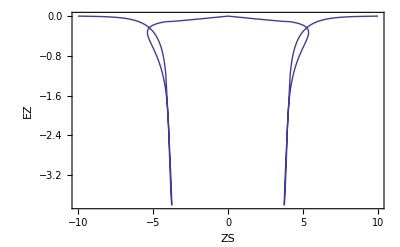

```mathematica
ListPlot[{#⟦1⟧, #⟦3⟧}&/@surfacedatraw, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"ZS", "EZ"}]
```

```mathematica
normalsurfacedat={1/100#⟦2⟧ (*x*),1/100#⟦1⟧(*z*),10^6 #⟦3⟧(*Enormal*), 1/μ0N#⟦4⟧(*Hphi*)}&/@surfacedatraw;
If[FLIP, normalsurfacedat={1/100#⟦2⟧ (*x*),-1/100#⟦1⟧(*z*),10^6 #⟦3⟧(*Enormal*),- 1/μ0N#⟦4⟧(*Hphi*)}&/@surfacedatraw;]
```

```mathematica
contour0={#[[zC]], #[[xC]]}&/@normalsurfacedat;

(*Use only non-reentrant part*)
p1=contour0⟦95⟧;
z1=Abs[p1⟦1⟧];
r1 =p1⟦2⟧;

d1=Select[contour0, Abs[#⟦1⟧]>=z1&& #⟦2⟧<r1&];
d2=Select[contour0, Abs[#⟦1⟧]<z1&];
contour1=Sort[Join[d1,d2], #1⟦1⟧<#2⟦1⟧&];

contourf=Interpolation[
contour1
];
```

```mathematica
Grid[{{"radius entrance (m)", contourf[-0.1]}
,{"radius exit(m)", contourf[0.1]}}, Frame->True]
```

radius entrance (m) | 0.02375
radius exit(m) | 0.02375

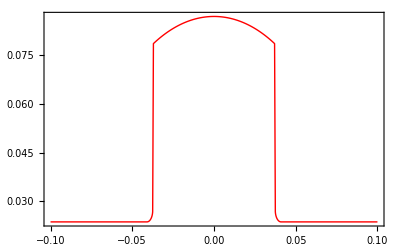

```mathematica
gcontour=ListPlot[contour1, Joined->True, Axes->False, PlotStyle->{Thick,Red},PlotRange->{All, {0, All}}]
```

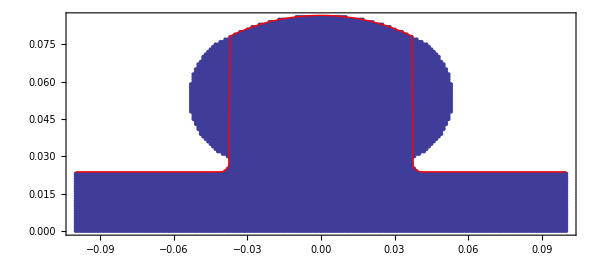

```mathematica
Show[ListPlot[{#[[zC]], #[[xC]]}&/@griddat, ImageSize->600], gcontour, AspectRatio->Automatic]
```

```mathematica
WallData[nsd_ (*normal surface dat*),  vecscale_]:=Module[{contour0,normaldat, Δz,Δr,θ, arrows, gArrows, gWall},
contour0={#⟦1⟧, #⟦2⟧}&/@nsd;
normaldat=Table[
Δz=( nsd[[i+1, zC]]-nsd[[i, zC]]);
Δr=( nsd[[i+1, xC]]-nsd[[i, xC]]);


θ=Arg[Δz+ⅈ Δr]; { nsd[[i,xC]], nsd⟦i,zC⟧,  - nsd⟦i,3⟧Cos[θ], nsd⟦i,3⟧Sin[θ], nsd⟦i,4⟧,-Sin[θ], Cos[θ] } , {i,1,Length[contour0]-1}];

arrows=Arrow[ {{#⟦2⟧, #⟦1⟧}, {#⟦2⟧+vecscale#⟦3⟧ , #⟦1⟧+vecscale#⟦4⟧ }}] &/@normaldat;
gArrows=Graphics[{Arrowheads[Small], arrows}];
gWall=Show[ListPlot[contour0], gArrows, AspectRatio->Automatic];
normaldat[[All,1;;5]]
];
```

```mathematica
walldat=WallData[normalsurfacedat, 0.000000001];
```

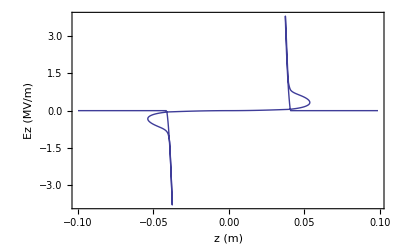

```mathematica
ListPlot[{#⟦zC⟧, 10^-6#⟦EzC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ez (MV/m)"}]
```

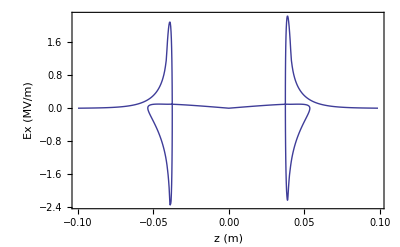

```mathematica
ListPlot[{#⟦zC⟧, 10^-6#⟦ExC⟧}&/@walldat, Joined->True, AxesOrigin->{0,0}, PlotRange->All, FrameLabel->{"z (m)", "Ex (MV/m)"}]
```

## Verify Grid

```mathematica
refdat=griddat;
```

```mathematica
Δz = 0.001;
Δx = 0.001;

nzpad=2;
nxpad=2;
```

```mathematica
xlist=Sort[#[[xC]]&/@refdat, #1<#2&];xlist=Intersection[xlist,xlist];tmpxmax=Max[xlist];xlist=Join[xlist, Table[tmpxmax+n Δx, {n,1,nxpad}]];
zlist=Sort[#[[zC]]&/@refdat, #1<#2&];zlist=Intersection[zlist,zlist];tmpzmax=Max[zlist];zlist=Join[zlist, Table[tmpzmax+n Δz, {n,1,nzpad}]];
xmax = Max[xlist];xmin = Min[xlist];xsize=xmax-xmin;
zmax = Max[zlist];zmin = Min[zlist];zsize=zmax-zmin;
```

```mathematica
Grid[{{,"min (m)","max (m)", "n_pts"},{"x: ",xmin,xmax, Length[xlist]}, {"z: ",zmin,zmax, Length[zlist]}}, Frame->True, Alignment->Left]
```

| min (m) | max (m) | n_pts
x:  | 0. | 0.088 | 89
z:  | -0.1 | 0.102 | 203

```mathematica
izof[z_]:=Round[(z -zmin)/Δz];
ixof[x_]:=Round[(x -xmin)/Δx];
zof[iz_]:=zmin + iz Δz;
xof[ix_]:=xmin + ix Δx;
```

```mathematica
ExGrid={izof[#[[zC]]],ixof[#[[xC]]], #⟦ExC⟧}&/@refdat;
```

```mathematica
izof[zmax]
```

202

```mathematica
ixof[xmax]
```

88

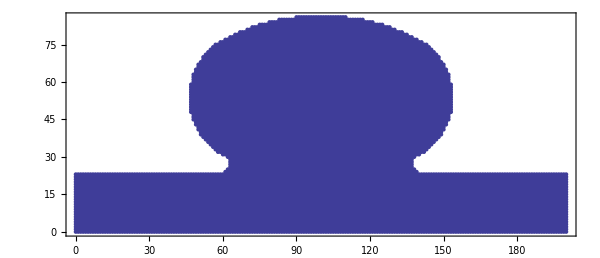

```mathematica
ListPlot[{izof[#[[zC]]],ixof[#[[xC]]]}&/@refdat, ImageSize->600, AspectRatio->Automatic]
```

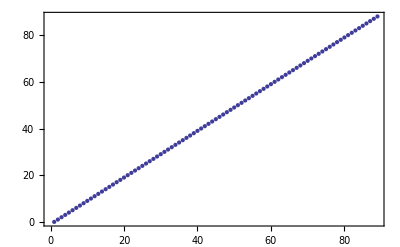

```mathematica
ListPlot[ixof/@xlist]
```

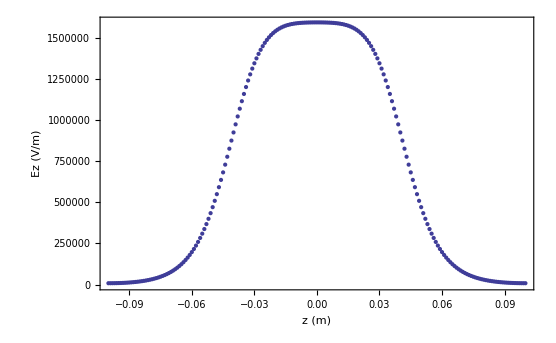

```mathematica
ListPlot[{#⟦zC⟧ ,#[[EzC]]}&/@Select[refdat, #⟦xC⟧==0&], FrameLabel->{"z (m)", "Ez (V/m)"}]
```

```mathematica
ListPointPlot3D[{{ixof[#⟦xC⟧],izof[#⟦zC⟧] ,#[[EzC]]}&/@refdat, {ixof[#⟦xC⟧],izof[#⟦zC⟧] ,#[[ExC]]}&/@refdat}, PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red}},AxesLabel->{"x index", "z index", "B (T)"}, BaseStyle->{FontSize->15}]
```

-Graphics3D-

## Make Bmad Grid

```mathematica
fieldmapdir =root;
tmpdir="~/Desktop/";
griddatafilename = outputCavityFilename;
wallfilename = outputWallFilename;
frequency  = 1.3 10^9(* Hz *);

axisdat=Select[refdat, #[[xC]]==0&];
maxEz0=Max[axisdat[[All,EzC]]];

setmaxEz0 =1.0;
fieldscale=setmaxEz0/maxEz0; 
note={"! Maximum on-axis Ez = "<>ToString[setmaxEz0, FortranForm]<>" V/m"};
```

```mathematica
(*pt format: pt(ir, iz) = ( (ErRe,ErIm), (0,0), (EzRe,EzIm), (0,0), (ErRe,ErIm), (0,0), (BϕRe, BϕIm) , (0,0) ) *)
MakeBmadGrid[dat_]:=Module[{header, body, ptlist},
header = {"{ "};
body = {
{"type = rotationally_symmetric_rz,"},
{"r0 = (",xmin,"," ,0 ,")," },
{"dr = (", Δx,",", Δz, "),"}
};

ptlist ={
"pt(", ixof[ #⟦xC⟧  ], "," ,izof[#⟦zC⟧]  ,") = ( ",
	"(" ,ToString[fieldscale*#⟦ExC⟧, FortranForm],", 0 ), (0,0), ",
			"(", ToString[fieldscale*#⟦EzC⟧, FortranForm],", 0 ), ",
	" (0,0), ( 0, ", ToString[fieldscale*#⟦ByC⟧, FortranForm] , "), (0,0))", ","}&/@dat;
ptlist[[-1,-1]] = "}";
Join[header,note, body,  ptlist]

]
```

```mathematica
(*Use additional extrapolated data*)
griddata=MakeBmadGrid[refdat ];
```

```mathematica
Export[tmpdir<>griddatafilename ,griddata, "Table", "FieldSeparators"->""];
Run["mv "<>tmpdir<>griddatafilename<>" "<>root<>griddatafilename];
```

### Wall file

```mathematica
zmax-zmin
```

0.202

```mathematica
nwallpoints = 500;
zmaxpad=0.004;
zrheader= {{"z(m)", "wall_radius(m)"}};
zrlist=Table[{z-zmin, contourf[z]}, {z, zmin, zmax-zmaxpad,((zmax-zmaxpad)-zmin)/(nwallpoints -1)}];Length[zrlist]
```

500

```mathematica
sectionheader={{bmadelename<>"[wall] = {"}};
sectionlist={"section = { s = ", #⟦1⟧, ", v(1) = {0.0, 0.0, " , #⟦2⟧, "} }," }&/@zrlist;
sectionlist[[-1,-1]] = "}}}";
```

```mathematica
(sectionheader~Join~sectionlist)[[1;;10]]
```

{{in.buncher[wall] = {},{section = { s = ,0.,, v(1) = {0.0, 0.0, ,0.02375,} },},{section = { s = ,0.000396794,, v(1) = {0.0, 0.0, ,0.02375,} },},{section = { s = ,0.000793587,, v(1) = {0.0, 0.0, ,0.02375,} },},{section = { s = ,0.00119038,, v(1) = {0.0, 0.0, ,0.02375,} },},{section = { s = ,0.00158717,, v(1) = {0.0, 0.0, ,0.02375,} },},{section = { s = ,0.00198397,, v(1) = {0.0, 0.0, ,0.02375,} },},{section = { s = ,0.00238076,, v(1) = {0.0, 0.0, ,0.02375,} },},{section = { s = ,0.00277756,, v(1) = {0.0, 0.0, ,0.02375,} },},{section = { s = ,0.00317435,, v(1) = {0.0, 0.0, ,0.02375,} },}}

```mathematica
Export[fieldmapdir <>wallfilename ,sectionheader~Join~sectionlist, "Table", "FieldSeparators"->""];
```

## Make GPT file for ASCI2GDF

```mathematica
gptdat=Select[refdat, ((Abs[#⟦zC⟧]≤ 0.1)&& #⟦xC⟧≤ 0.018 )&];
```

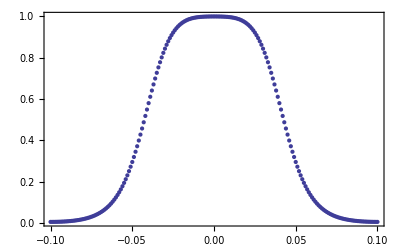

```mathematica
ListPlot[{#⟦zC⟧,fieldscale #⟦EzC⟧}&/@Select[gptdat, #⟦xC⟧==0&], PlotRange->All]
```

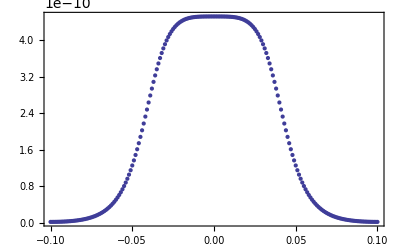

```mathematica
(*Note that GPT takes E columns oscillating as cos(ωt), and the B column oscillating as -sin(ωt).
*)
ListPlot[{#⟦zC⟧,- 1fieldscale#⟦ByC⟧}&/@Select[gptdat, #⟦xC⟧==0.01&], PlotRange->All]
```

```mathematica
gptlabels={
{"# New buncher cavity"},
{"# On-axis Ez scaled to 1 V/m"},
{"# R(m)", "Z(m)",  "Er(V/m)", "Ez(V/m)", "Bphi(T)"},
{"R", "Z", "Er", "Ez", "Bphi"}
};
```

```mathematica
gptoutdat={#⟦xC⟧, #⟦zC⟧,fieldscale #⟦ExC⟧,fieldscale#⟦EzC⟧,-1 fieldscale#⟦ByC⟧}&/@gptdat;
```

```mathematica
file="buncher_CTB_new_for_ASCI2GDF.txt";
Export[tmpdir<>file, Join[gptlabels, gptoutdat], "Table"];
Run["mv "<>tmpdir<>file<>" "<>root<>file]
```

0

## EM Field query

```mathematica
fieldquerydir=root
```

/Volumes/user/cem52/erl/CERL/lattice_devel/Phase1B/model/a1/buncher/

```mathematica
it = 1;
ix = 2;
iy =3;
is = 4;
iEx=5;
iEy=6;
iEs=7;
iBx=8;
iBy=9;
iBs=10;
```

### Field on axis

```mathematica
selebeg=0.1;

smin =0+selebeg;
smax = 0.2+selebeg
myt=0;
myx=0.00;
myy=0.0;
sampledat=Table[{myt, myx, myy, s}, {s, smin, smax, (smax-smin)/100}];
Export[root<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"]
```

0.3

/Volumes/user/cem52/erl/CERL/lattice_devel/model/in_grid/buncher/querypoints.dat

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];
```

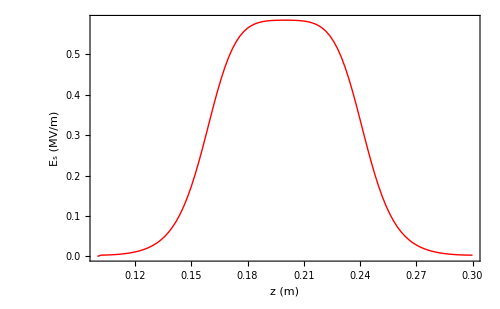

```mathematica
g1=ListPlot[{#[[is]],  10^-6#[[iEs]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Red];
Show[g1, PlotRange->All, FrameLabel->{"z (m)", "E_s (MV/m)"}, ImageSize->500]
```

### Field in time

```mathematica
freq=(1.3 10^9);

tmin=0;
tmax = 1/(1.3 10^9);
mys = 0.25;
myx=0.02;
myy=0.0;
sampledat=Table[{t, myx, myy, mys}, {t, tmin, tmax, (tmax-tmin)/100}];
Export[root<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"]
```

/Volumes/user/cem52/erl/CERL/lattice_devel/Phase1B/model/a1/buncher/querypoints.dat

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];
```

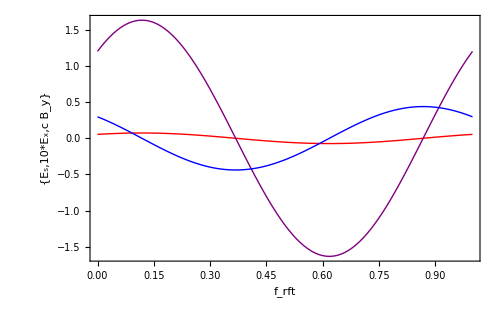

```mathematica
g1=ListPlot[{
{#[[it]]*freq,  10^-6#[[iEs]]}&/@dat,
{#[[it]]*freq,  10 10^-6#[[iEx]]}&/@dat,
{#[[it]]*freq, 10  10^-6 cLightN#[[iBy]]}&/@dat
}, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->{Red,Purple, Blue}];
Show[g1, PlotRange->All, FrameLabel->{"f_rft",{ Style["E_s",Red], Style["10*E_x",Purple], Style["c B_y", Blue]}}, ImageSize->500]
```

### Field on a flat grid

```mathematica
selebeg=0.1;

smin =0+selebeg;
smax = 0.2+selebeg;
myt=0;
xmin=0;
xmax = 0.05;
nx=50;
ns=200;
xstep=(xmax-xmin)/(nx-1);
 sstep=(smax-smin)/(ns-1);

isof[s_]:=Round[(s-smin)/sstep];
ixof[x_]:=Round[(x -xmin)/xstep];
zof[is_]:=smin + is sstep;
xof[ix_]:=xmin + ix xstep;

sampledat=Flatten[Table[{myt, x, myy, s}, {x,xmin,xmax,xstep},{s, smin, smax,sstep}], 1];Length[sampledat]
```

10000

```mathematica
Export[tmpdir<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"];
Run["mv "<>tmpdir<>"querypoints.dat"<>" "<>root<>"querypoints.dat"];
```

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];Length[dat]
```

10000

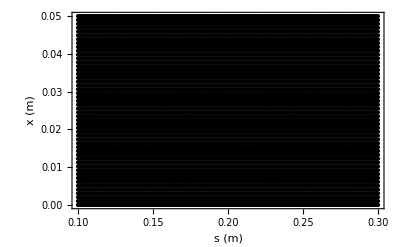

```mathematica
ListPlot[ {#[[is]], #[[ix]]}&/@dat, Frame->True, FrameLabel->{"s (m)", "x (m)"}, BaseStyle->{FontSize->15}, PlotStyle->Black]
```

```mathematica
ListPointPlot3D[{{#⟦is⟧, #⟦ix⟧, #⟦iEs⟧}&/@dat, {#⟦is⟧, #⟦ix⟧, #⟦iEx⟧}&/@dat} , PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red}}]
```

-Graphics3D-

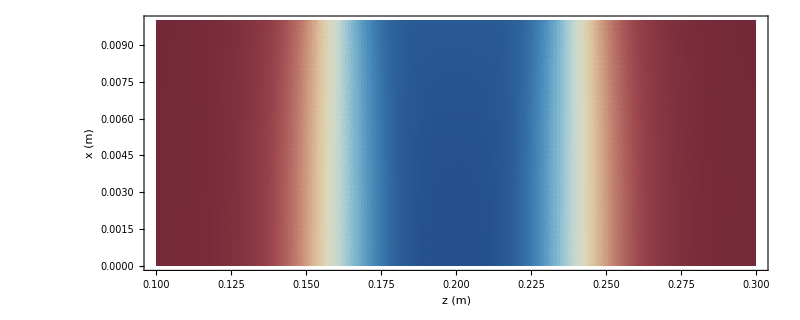

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iEs⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax}}, ColorFunction->"RedBlueTones", FrameLabel->{"z (m)", "x (m)"}],ImageSize->800]
```

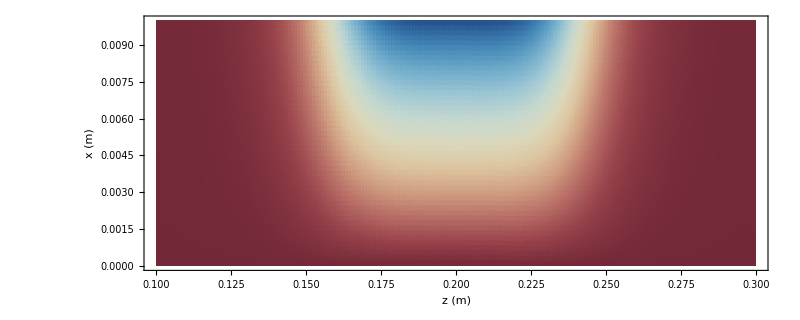

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iBy⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax},All}, ColorFunction->"RedBlueTones",FrameLabel->{"z (m)", "x (m)"}, PlotRange->All],ImageSize->800]
```